```mathematica
ClearAll["Global`*"]
```

```mathematica
Remove[starvation,M,B0,Bm,η,γ,f0,Em]
starvation =  ts*-Bm/(Em*Log[1-f0*M^(γ-1)]);
recovery = ts*- ((η-1)*Bm/Em)/(Log[1-(M*(B0/Bm)^(1/(η-1)))^(1-η)]-Log[1 - (M*(1-f0*M^(γ-1))*(B0/Bm)^(1/(η-1)))^(1-η)]);
Ratio = FullSimplify[starvation/recovery]
```

(Log[1-((B0/Bm)^(1/(-1+η)) M)^(1-η)]-Log[1-((B0/Bm)^(1/(-1+η)) (M-f0 M^γ))^(1-η)])/((-1+η) Log[1-f0 M^(-1+γ)])

```mathematica
Ratesfunc[x_] :=(
noise=x[[1]];
ts=x[[2]];
M=x[[3]];
B0=x[[4]];
Bm=x[[5]];
Em=x[[6]];
η=x[[7]];
η2=x[[8]];
λ0=x[[9]];
ef=x[[10]];
γ=x[[11]];
ζ=x[[12]];
f0=x[[13]];
mm0=x[[14]];
growth =N[ts* λ0*M^η2]*(1+RandomReal[{-noise,noise}]) ;
starvation =  N[ts*-Bm/(Em*Log[1-f0*M^(γ-1)])]*(1+RandomReal[{-noise,noise}]);
mortality =N[ts*-Bm/(Em*Log[1-(f0*M^γ+ mm0*M^ζ)/M])]*(1+RandomReal[{-noise,noise}]);
recovery =N[ ts*- ((η-1)*Bm/Em)/(Log[1-(M*(B0/Bm)^(1/(η-1)))^(1-η)]-Log[1 - (M*(1-f0*M^(γ-1))*(B0/Bm)^(1/(η-1)))^(1-η)])]*(1+RandomReal[{-noise,noise}]);
maintenance = (ts*ef*B0*M^η)*(1+RandomReal[{-noise,noise}]);
resourcegrowth = ts*0.5*(1+RandomReal[{-noise,noise}]);

{growth,starvation,mortality,recovery,maintenance,resourcegrowth}
)
```

```mathematica
MetapopDyn[α_,λ_,σ_,ρ_,β_,μ_,T_,F0_,H0_,R0_] :=

NDSolve[{
F'[t] ==λ*F[t]-σ*(1-R[t])*F[t] +ρ* R[t] * H[t],
H'[t] ==σ*(1-R[t])*F[t] - ρ* R[t]*H[t] - μ*H[t],
R'[t] ==α*R[t]*(1-R[t]) -(ρ*H[t] + β*F[t])*R[t] ,
F[0]==F0,H[0]==H0,R[0]==R0},{F,H,R},{t,0,T},MaxSteps->Infinity,InterpolationOrder->All];
TestThreshold[timeseries_,threshold_]:=If[AnyTrue[timeseries,#<threshold&],1,0];
parameters={
(*noise*)0,
(*ts*)1,
(*M*)Mass =10^2,
(*B0*)1.9*10^(-2),
(*Bm*)0.0245,
(*Em*)21.39/2*1000(*J/gram*),
(*η*)3/4,
(*η2*)-0.206,
(*λ0*)3.3879*10^(-7),
(*ef*)0.001,
(*γ*)1.19,
(*ζ*)1.01,
(*f0*)0.0202,
(*mm0*)0.324};
RF =Ratesfunc[parameters];
growth=RF[[1]];
starvation=RF[[2]];
mortality=RF[[3]];
recovery=RF[[4]];
maintenance=RF[[5]];
resourcegrowth=RF[[6]];
(*rhovalues = Table[x,{x,0.2,0.7,0.1}];*)
(*scalevalues = Table[x,{x,6,0.5,-0.6}];*)
(*sigmavalues =Table[x,{x,starvation/200,starvation/0.4,0.0000005}];*)
sigmavalues = RecurrenceTable[{B[n+1] == B[n]+1/50B[n],B[1]==2.3060191710825582*^-7},B,{n,1,300}];
ExtinctionSigma = ParallelTable[
Reps = 500;
ProportionExtinct=With[{
α=resourcegrowth,λ=growth,σ=sigma,ρ=recovery,β=maintenance,μ=mortality,T=100000000,threshold=10,PercentPerturbed=1},
ExtinctionReps = Table[
F0=(α λ μ (μ+ρ))/((β μ+λ ρ) (λ ρ+μ σ))*(1+RandomReal[{-PercentPerturbed,PercentPerturbed}]);
H0=(α λ^2 (μ+ρ))/((β μ+λ ρ) (λ ρ+μ σ))*(1+RandomReal[{-PercentPerturbed,PercentPerturbed}]);
R0= (μ (-λ+σ))/(λ ρ+μ σ)*(1+RandomReal[{-PercentPerturbed,PercentPerturbed}]);
(*F0=RandomReal[{1000,30000}];
H0 = RandomReal[{1000,30000}];
R0 = RandomReal[{1000,30000}];*)
(*Traj=Evaluate[{F[t],H[t],R[t]}/.MetapopDyn[α,λ,σ,ρ,β,μ,T,F0,H0,R0] ]*)
Traj=Table[Evaluate[{F[t],H[t],R[t]}/.MetapopDyn[α,λ,σ,ρ,β,μ,T,F0,H0,R0]],{t,0,100000000,100000}];
Ftraj = Flatten[Traj,1][[100;;1000,1]];
Htraj = Flatten[Traj,1][[100;;1000,2]];
Rtraj = Flatten[Traj,1][[100;1000,3]];
ConsumerDensity = Htraj + Ftraj;
Extinct=TestThreshold[ConsumerDensity,threshold],
{Reps}];
{sigma/ρ,N[Total[ExtinctionReps]/Reps]}
],
{sigma,sigmavalues}(*,{rho,rhovalues}*)];
```

NDSolve::nderr: Error test failure at t == 8.53261×10^7; unable to continue.

InterpolatingFunction::dmval: Input value {85400000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::ndsz: At t == 44.7606, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 1.54191×10^7, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {85400000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {100000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::ndsz: At t == 1.68073×10^6, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {15500000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {85400000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {100000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1700000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {15500000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {100000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1700000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {15500000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::nderr: Error test failure at t == 6.90819×10^7; unable to continue.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1700000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 15.2747, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 18.1661, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 2.11041×10^6, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 129.901, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 15.9087, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 614397., step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 391569., step size is effectively zero; singularity or stiff system suspected.

NDSolve::nderr: Error test failure at t == 7.19678×10^7; unable to continue.

General::stop: Further output of NDSolve :: ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 5.47887×10^6, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve :: ndsz will be suppressed during this calculation.

General::stop: Further output of NDSolve :: nderr will be suppressed during this calculation.

General::stop: Further output of NDSolve :: ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 16.1117, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve :: ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 1.06898×10^6, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {1100000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 1.98025×10^6, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 5.83669×10^6, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve :: ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 640904., step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {700000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 226812., step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 1.30905×10^6, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve :: ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 1.3779×10^6, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {1400000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 411664., step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 286632., step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve :: ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 242490., step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {300000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 175879., step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 222446., step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve :: ndsz will be suppressed during this calculation.

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Mathematica/ExtinctionSigmaRhoAllometry.dat",ExtinctionSigma]
```

/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Mathematica/ExtinctionSigmaRhoAllometry.dat

```mathematica
ExtinctionSigma=ToExpression[Import["/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Mathematica/ExtinctionSigmaRhoAllometry.dat","Data"]];
```

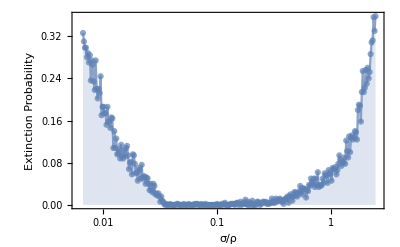

```mathematica
ExtinctionsAllometricPlot=Show[{
ListLogLinearPlot[ExtinctionSigma,PlotRange->{{0.006,2.6},{0,All}},PlotStyle->Directive[Opacity[0.7]],Frame->True,FrameLabel->{"σ/ρ","Extinction Probability"}],
ListLogLinearPlot[ExtinctionSigma,PlotRange->{0,1},Joined->True,Filling->Bottom,PlotStyle->Directive[Opacity[0.7]]](*,
step=10;If[EvenQ[step],step=step+1];
ListLogLinearPlot[
MovingAverage[
Re[ExtinctionSigma],step],PlotStyle->ColorData[97,8],Joined->True(*Transpose[{Re[ExtinctionSigma[[1+IntegerPart[N[step/2]];;Length[ExtinctionSigma]-IntegerPart[N[step/2]],1]]],MovingAverage[ExtinctionSigma[[All,2]],step]}],PlotStyle->ColorData[97,8],Joined->True*)
]*)
},ImageSize->400]
```

```mathematica
Ratio
```

(Log[1-((B0/Bm)^(1/(-1+η)) M)^(1-η)]-Log[1-((B0/Bm)^(1/(-1+η)) (M-f0 M^γ))^(1-η)])/((-1+η) Log[1-f0 M^(-1+γ)])

```mathematica
RatioValues=(
noise=0.2;
ParallelTable[
value=Re[Ratio/.{
M->10^2,
η->3/4,
γ->1.19,
f0->0.0202*(1+RandomReal[{-noise,noise}]),
B0->1.9*10^(-2)*(1+RandomReal[{-noise,noise}]),
Bm->0.0245*(1+RandomReal[{-noise,noise}])
}];
{value,i},
{i,0.1,10,0.001}]
);
```

```mathematica
RatioValuePlot=ListLogLinearPlot[RatioValues,PlotRange->{{0.006,2.6},All},FrameTicks->None,Frame->True,AspectRatio->1/10,PlotStyle->Directive[{Opacity[0.05]}]]
```

-Graphics-

```mathematica
RatioValues
```

{{1.35356,0.1},{1.34833,0.101},{1.39773,0.102},{1.28398,0.103},{1.3558,0.104},{1.38816,0.105},9890,{1.2817,9.996},{1.35395,9.997},{1.2882,9.998},{1.34111,9.999},{1.2923,10.}}
 |  |  |  |

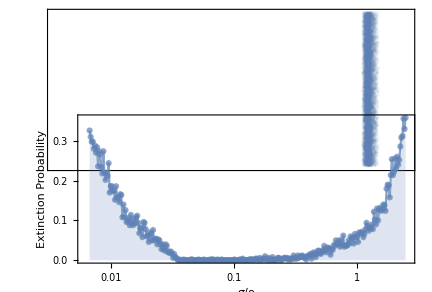

```mathematica
CombinedAllometricPlot=GraphicsColumn[{
Show[RatioValuePlot,ImagePadding->{{43,14},{Automatic,Automatic}}],
Show[
ExtinctionsAllometricPlot,ImagePadding->{{40,10},{Automatic,Automatic}}]},Spacings->Scaled[-0.65],ImagePadding->{{0,0},{110,40}}]
```

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/fig_ExtinctionAllometric.pdf",CombinedAllometricPlot,"PDF",ImageResolution->300]
```

/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/fig_ExtinctionAllometric.pdf

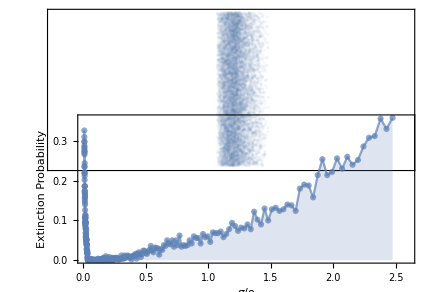

```mathematica
ExtinctionsAllometricPlot2=Show[{
ListPlot[ExtinctionSigma,PlotRange->{{0.006,2.6},{0,All}},PlotStyle->Directive[Opacity[0.7]],Frame->True,FrameLabel->{"σ/ρ","Extinction Probability"}],
ListPlot[ExtinctionSigma,PlotRange->{0,1},Joined->True,Filling->Bottom,PlotStyle->Directive[Opacity[0.7]]](*,
step=10;If[EvenQ[step],step=step+1];
ListLogLinearPlot[
MovingAverage[
Re[ExtinctionSigma],step],PlotStyle->ColorData[97,8],Joined->True(*Transpose[{Re[ExtinctionSigma[[1+IntegerPart[N[step/2]];;Length[ExtinctionSigma]-IntegerPart[N[step/2]],1]]],MovingAverage[ExtinctionSigma[[All,2]],step]}],PlotStyle->ColorData[97,8],Joined->True*)
]*)
},ImageSize->400];
RatioValuePlot2=ListPlot[RatioValues,PlotRange->{{0.006,2.6},All},FrameTicks->None,Frame->True,AspectRatio->1/10,PlotStyle->Directive[{Opacity[0.05]}]];
CombinedAllometricPlot=GraphicsColumn[{
Show[RatioValuePlot2,ImagePadding->{{43,14},{Automatic,Automatic}}],
Show[
ExtinctionsAllometricPlot2,ImagePadding->{{40,10},{Automatic,Automatic}}]},Spacings->Scaled[-0.65],ImagePadding->{{0,0},{110,40}}]
```